Diplomado En Programación Básica
Universidad Autónoma de Chiapas
Centro Mesoamericano de Física Teórica

Michael Steven Paucar Rojas

# MATHEMATICA

-Graphics-

## 1. Introducción

El presente cuaderno constituye un recurso de apoyo para el aprendizaje de Mathematica orientado a la programación y al uso de sus principales funciones en contextos académicos y prácticos. El contenido se organiza de manera progresiva iniciando con operaciones básicas sobre listas, expresiones matemáticas y representaciones gráficas para avanzar hacia temas más complejos como manejo de entidades, conversiones de unidades, generación de visualizaciones interactivas y aplicaciones en análisis de datos.

El enfoque seguido combina teoría con ejemplos prácticos que buscan ilustrar no solo la sintaxis del lenguaje sino también la lógica detrás de cada comando. Se ha procurado mantener una estructura clara donde cada sección incluye subtítulos, descripciones y comentarios en el código para facilitar la comprensión. Esto permite que el material pueda ser utilizado tanto por estudiantes en formación como por interesados en explorar las capacidades del software en distintos escenarios.

Cabe señalar que el documento reúne apuntes propios sistematizados a partir del estudio y la práctica personal. Estos apuntes no reemplazan la documentación oficial de Mathematica pero sí constituyen un complemento útil para guiar el aprendizaje y servir como referencia en la resolución de ejercicios y proyectos futuros.

## 2. Tabla de contenidos

Introducción

Tabla de contenidos

Clase 1 — Introducción a Wolfram Mathematica

Captura y análisis de imagen

Clase 2 — Comandos básicos, listas y entidades

Comandos del sistema

Comandos interactivos

Entidades: países y banderas

Exploración planetaria

Conversiones de unidades y monedas

Listas: creación y operaciones básicas

Funciones para secuencias y combinación de listas

Manipulación avanzada de listas

Funciones adicionales sobre listas

Clase 3 — Gráficos, colores y funciones trigonométricas

Gráficas estadísticas (barras y pastel)

Selección y manipulación de datos para visualización

Colores y estilos gráficos (paletas y transformaciones)

Funciones matemáticas básicas y plots elementales

Tareas

Tarea 1 — Cálculos Numéricos y Funciones en Mathematic

Tarea 2 — Formato de Notebook

Apéndice

Comandos comunes

## 3. Clase 1 — Introducción a Wolfram Mathematica

📆 2025/09/17

⚡ Introducción: Presentación general de Mathematica y primeras pruebas con entrada de imágenes y herramientas de visión.

## 3.1. Captura y análisis de imagen

📌 Explicación: se muestra cómo capturar una imagen desde la cámara (CurrentImage) y cómo aplicar una función de análisis facial (FacialFeatures). 
Para detalles de CurrentImage y FacialFeatures ver ‘Comandos comunes’.

# Capturar imagen desde la cámara

```mathematica
yo=CurrentImage[]
```

-Graphics-

# Detectar rasgos faciales en la imagen

```mathematica
FacialFeatures[yo]
```

{<|Image→-Graphics-,Age→24,Gender→Female,Emotion→neutral|>}

💎 Nota: El análisis facial proporciona una edad aproximada y puede intentar identificar el género de la persona en la imagen. Sin embargo, los resultados pueden no ser precisos, y es posible que se necesiten varios intentos para obtener una estimación más acertada.

## 4. Clase 2 — Comandos básicos, listas y entidades

📆 2025/09/22

⚡ Introducción: En esta sesión se trabajan comandos de sistema y de interacción, acceso a la Wolfram Knowledgebase (entidades), conversión de unidades y manipulación básica y avanzada de listas. Cada bloque contiene comentarios inline para facilitar la lectura.

## 4.1. Comandos del sistema

📌 Explicación: funciones para fijar directorio de trabajo y consultar la fecha/hora del sistema. 
Ver Comandos comunes para definiciones.

# Define o consulta el directorio de trabajo

```mathematica
SetDirectory[]
```

C:\Users\IBM

# Devuelve fecha y hora actual

```mathematica
Date[]
```

{2025,9,23,22,46,39.8336576}

## 4.2. Comandos interactivos

📌 Explicación: salida de voz y botones interactivos para respuestas en tiempo real.

# Convierte el texto a audio y reproduce “Hola Mundo”

```mathematica
Speak["Hola Mundo"]
```

# Reproduce “Hello Wolfram” mediante síntesis de voz

```mathematica
Speak["Hello Wolfram"]
```

# Crea un botón que al presionarlo ejecuta Speak[“Thank you”]

```mathematica
Button["Presioname", Speak[Thank You]]
```

Presioname

💎 Nota: Button crea controles interactivos; ejecuta la acción cuando se presiona. 
Ver ‘Comandos comunes’ para más usos de Button y Speak.

## 4.3. Entidades: países y banderas

📌 Explicación:  uso de la Wolfram Knowledgebase Entity para recuperar información de países y sus banderas

# Crea la entidad correspondiente al país’Ecuador’

```mathematica
Entity["Country", "Ecuador"]
```

Ecuador

# Extrae la imagen de la bandera de la entidad país

```mathematica
Entity["Country", "Ecuador"]["Flag"]
```

-Graphics-

# Devuelve una lista de imágenes/flags para los países listados.

```mathematica
EntityValue[{Entity["Country", "UnitedStates"], Entity["Country", "Brazil"], Entity["Country", "China"]}]
```

{Estados Unidos,Brasil,República Popular China}

# Obtener banderas de múltiples países


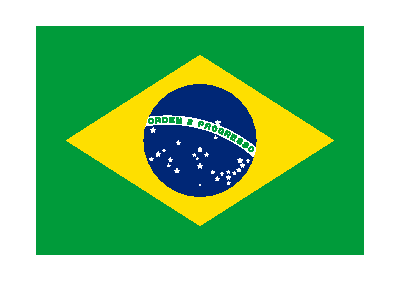

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[{Entity["Country", "UnitedStates"], Entity["Country", "Brazil"], Entity["Country", "Ecuador"], Entity["Country", "China"],Entity["Country", "Mexico"]}, "Flag"]
```

## 4.4. Exploración planetaria

📌 Explicación:  listar entidades de tipo planeta y recuperar sus imágenes u otras propiedades.

# Lista todas las entidades que pertenecen a la clase’Planet’

```mathematica
EntityList[EntityClass["Planet", All]]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

# Recupera la imagen asociada a cada planeta listado

```mathematica
EntityValue[EntityClass["Planet", All], "Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 4.5. Conversiones de unidades y monedas

📌 Explicación: trabajo con Quantity y UnitConvert para convertir y simplificar unidades; CurrencyConvert para divisas.

# Convierte 2.6 horas a minutos

```mathematica
UnitConvert[Quantity[2.6,  "Hours"], "Minutes"]
```

156. min

# Suma cantidades con unidades distintas;Mathematica maneja la conversión interna

```mathematica
Quantity[7.5, "Feet"] + Quantity[14, "Centimeters"]
```

242.6 cm

# Simplifica la unidad si es posible (ej.:a metros)

```mathematica
UnitSimplify[Quantity[242.6, "Centimeters"]]
```

2.426 m

# Convierte 100 liras turcas a USD usando tasa actual;puede requerir conexión

```mathematica
CurrencyConvert[Quantity[100., "TRY"], Quantity[1, "USDollars"]]
```

2.41 $

# Convierte dólares a centavos estadounidenses

```mathematica
UnitConvert[Quantity[5.12363, "USDollars"], "USCents"]
```

512.363 ¢

# Convierte 5 pulgadas a centímetros y devuelve número aproximado

```mathematica
N[UnitConvert[Quantity[5, "Inches"], "Centimeters"]]
```

12.7 cm

💎 Nota: CurrencyConvert puede necesitar conexión a internet para obtener tipos de cambio actualizados.

## 4.6. Listas: creación y operaciones básicas

📌 Explicación: definición de listas, operaciones escalares, limpieza de variables y gráficas sencillas.

📋 Declaración de listas:

{} (llaves) → Sirven para definir listas.

```mathematica
lista={2,4,6,8}
```

{2,4,6,8}

Sin llaves → Se usa cuando una función espera un rango o expresión directamente, no un conjunto de valores.

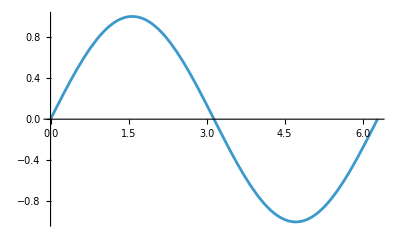

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

Aquí los límites {x,0,2 Pi} son un rango, no una lista de valores discretos.

🔒 Regla práctica:

Usa llaves {} cuando quieras pasar conjuntos de valores discretos ({1,2,3}).

Usa sin llaves o rangos {var,min,max} cuando definas un intervalo continuo.

# Elimina cualquier valor previo de la variable a

```mathematica
Clear[a]
```

# Asigna una lista a ’a’

```mathematica
a = {2, 6, 8, 9, 10}
```

{2,6,8,9,10}

# Asigna una lista a ’b’

```mathematica
b = {5, 8, 9, 5}
```

{5,8,9,5}

# Escalar por lista

```mathematica
3 * a
```

{6,18,24,27,30}

```mathematica
Clear[a]
```

```mathematica
a
```

a

```mathematica
a * 5
```

5 a

# Grafica los valores de la lista como puntos/serie

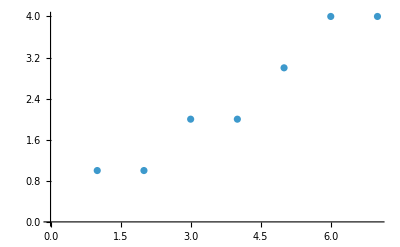

```mathematica
ListPlot[{1, 1, 2, 2, 3, 4, 4}]
```

# Gráfico mejorado  con los valores de la lista como puntos/serie

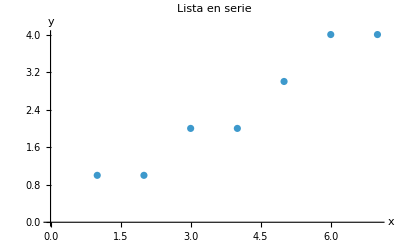

```mathematica
Show[%33,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[Lista en serie],LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0],Italic}]
```

## 4.7. Funciones para secuencias y combinación de listas

📌 Explicación: generar rangos, invertir, unir listas y visualizar secuencias. 
Ver ‘Comandos comunes’ para info sobre Range, Join y Reverse.

```mathematica
?Range
```

⭐ El ‘?comando’, muestra la ayuda o documentación para la función Range.

# Genera la lista {1,2,...,25}

```mathematica
Range[25]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

# Grafica la secuencia 1..20

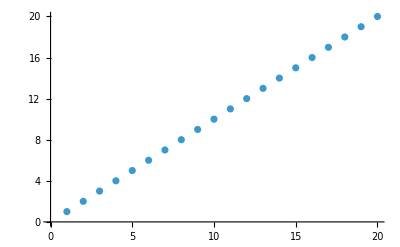

```mathematica
ListPlot[Range[20]]
```

# Invierte el orden:devuelve {4,3,2,1}

```mathematica
Reverse[{1, 2, 3, 4}]
```

{4,3,2,1}

# Une dos listas:{1,2,3,6}

```mathematica
Join[{1, 2, 3}, {6}]
```

{1,2,3,6}

📌 Explicación:  Join concatena listas sin eliminar duplicados; para obtener unión única usa Union.

# Une {1,2,3} con {1,2,3,4,5}->{1,2,3,1,2,3,4,5}

```mathematica
Join[Range[3], Range[5]]
```

{1,2,3,1,2,3,4,5}

🎯 Reto en clase — Listas
Resolver los ejercicios con funciones de Listas.

Salida esperada {1, 2, 3, 4, 5, 3, 2, 1, 10, 15}

# Función Join:
	# La función `Join` se utiliza para combinar varias listas en una sola.

# Rango de números (Range):
	# `Range[5]` genera una lista de números desde 1 hasta 5, es decir, {1, 2, 3, 4, 5}.
	# `Reverse[Range[3]]` primero genera la lista {1, 2, 3} y luego la invierte, resultando en {3, 2, 1}.
	# `{10, 15}` es simplemente una lista con los números 10 y 15.

# Resultado:
	# El resultado de `Join` es la combinación de las tres listas mencionadas:
	# {1, 2, 3, 4, 5}, {3, 2, 1} y {10, 15}.
	# La lista final será: {1, 2, 3, 4, 5, 3, 2, 1, 10, 15}.

```mathematica
Join[Range[5], Reverse[Range[3]], {10, 15}]
```

{1,2,3,4,5,3,2,1,10,15}

Salida esperada {5, 6, 7, 8, 1, 2, 4, 5, 4, 3}

# Función Join:
	# La función `Join` se utiliza para combinar varias listas en una sola.

# Rango de números (Range):
	# `Range[5, 8]` genera una lista de números desde 5 hasta 8, es decir, {5, 6, 7, 8}.
	# `Range[5]` genera una lista de números desde 1 hasta 5, es decir, {1, 2, 3, 4, 5}.
	# `{4, 3}` es una lista con los números 4 y 3.

# Resultado:
	# El resultado de `Join` es la combinación de las tres listas mencionadas:
	# {5, 6, 7, 8}, {1, 2, 3, 4, 5} y {4, 3}.
	# La lista final será: {5, 6, 7, 8, 1, 2, 3, 4, 5, 4, 3}.

```mathematica
Join[Range[5,8], Range[5], {4, 3}]
```

{5,6,7,8,1,2,3,4,5,4,3}

💎 Nota: También se puede ordenar, contar repeticiones (Count), graficar (ListPlot), extraer sublistas (Take, Drop).

## 4.8. Manipulación avanzada de listas

📌 Explicación: técnicas para construir listas complejas y comprobar pertenencia o patrones.

# Crea lista combinada:{1,2,3,6}

```mathematica
list = Join[{1, 2, 3}, {6}]
```

{1,2,3,6}

# Devuelve True si 6 está en ’list’

```mathematica
MemberQ[list, 6]
```

True

# Construye una lista concatenando transformaciones de Range

```mathematica
Join[Range[4] + 4, Range[2], Range[2] + 3, {3}]
```

{5,6,7,8,1,2,4,5,3}

# Variante que incluye Reverse para cambiar orden de una parte

```mathematica
Join[Range[4] + 4, Range[2], Range[2] + 3, Reverse[Range[2]+2]]
```

{5,6,7,8,1,2,4,5,4,3}

# Grafica la concatenación de tres secuencias 1..20 (serie repetida)

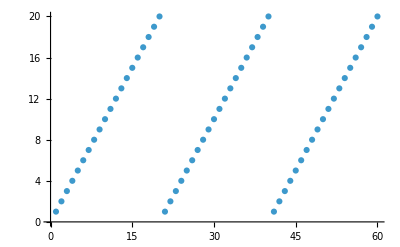

```mathematica
ListPlot[Join[Range[20], Range[20], Range[20]]]
```

## 4.9. Funciones adicionales sobre listas

📌 Explicación: varias funciones pequeñas pero muy útiles para análisis rápido de listas y números.
Funciones útiles: conteo, orden, extracción.

# Genera la lista 1..100

```mathematica
Range[10^2]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

# Ordena la lista ascendentemente

```mathematica
Sort[{4, 2, 1, 3, 6}]
```

{1,2,3,4,6}

# Devuelve la longitud de la lista

```mathematica
Length[{5, 4, 5, 3, 4, 5}]
```

6

# Suma todos los elementos de la lista

```mathematica
Total[{1, 2, 2, 2}]
```

7

# Suma 1..10->55

```mathematica
Total[Range[10]]
```

55

# Cuenta cuántas veces aparece’b’ (simbolos/elementos)

```mathematica
Count[{a, a, a, a, c, b, a}, b]
```

1

# Devuelve el primer elemento

```mathematica
First[{7, 6, 5}]
```

7

# Devuelve el último elemento

```mathematica
Last[{7, 6, 5}]
```

5

# Ordena y devuelve el primero (mínimo)

```mathematica
First[Sort[{6, 7, 1, 2, 4, 5}]]
```

1

# Devuelve el mínimo de la lista

```mathematica
Min[{6, 7, 1, 2, 4, 5}]
```

1

# Devuelve {1,9,8,8}

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

# Devuelve el último dígito:8

```mathematica
Last[IntegerDigits[1988]]
```

8

# Crea {1,2,3,4,4,3,2,1} con Join

```mathematica
Join[Range[4], Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

# Genera una secuencia 1..k con k aleatorio entre 0 y 30

```mathematica
Range[RandomInteger[30]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

💎 Nota: Estas funciones son atómicas para análisis y resumen de datos; úsalas dentro de pipelines con Map, Select y Fold para tareas más avanzadas.

```mathematica
CellPrint[Cell["","PageBreak",CellVisible->False]]
```

## 5. Clase 3 — Gráficos, colores y funciones trigonométricas

📆 2025/09/17

⚡ Introducción: En esta sesión trabajamos visualización en 2D y 3D (barras, pastel), manejo de colores y estilos, y gráficas de funciones matemáticas y trigonométricas (normales e inversas). Se incluyen notas sobre límites de dominio y opciones de presentación para obtener gráficos listos para exportar.

## 5.1. Gráficas estadísticas (barras y pastel)

📌 Explicación: ejemplos con BarChart y PieChart en 2D y 3D. Útiles para visualizar distribuciones de frecuencia o categorías.

📊 Opciones de gráficos
Las funciones gráficas (PieChart, BarChart, Plot, etc.) aceptan opciones para personalizar estilo, etiquetas y apariencia.

```mathematica
PieChart3D[{8,9,6,8,1,3,7,4},ChartElementFunction->"CylindricalSector3D",ChartStyle->{Red,Purple,Green,Blue,Orange,Yellow,Cyan,Gray},ChartLegends->{"Rojo","Morado","Verde","Azul","Naranja","Amarillo","Cian","Gris"}]
```

-Graphics3D-

📌 Explicación:

ChartElementFunction -> “CylindricalSector3D” → Cambia la forma del sector en 3D.

ChartStyle -> {...} → Aplica colores definidos a cada porción.

ChartLegends -> {...} → Añade leyendas personalizadas con etiquetas.

🎨 Estilo de texto y fuentes: Style[texto, opciones] — Cambia fuente, tamaño, color, etc.

```mathematica
Style["Texto en azul y grande",Blue,18,Bold]
```

Texto en azul y grande

🔎 Opciones comunes:

FontSize -> n

FontColor -> Color

FontFamily -> “Arial”

Bold, Italic

# En gráficos, puedes integrarlo en etiquetas y títulos

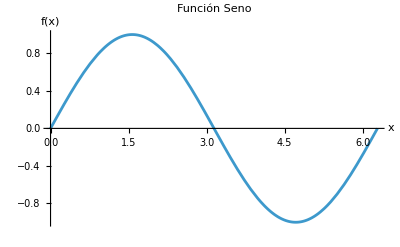

```mathematica
Plot[Sin[x],{x,0,2 Pi},PlotLabel->Style["Función Seno",16,Bold,Blue],AxesLabel->{Style["x",14],Style["f(x)",14,Italic]}]
```

🏷️ Etiquetas en gráficos:

PlotLabel -> “texto” → Título del gráfico.

AxesLabel -> {“x”,”y”} → Nombres de ejes.

ChartLegends -> {“etiqueta1”,”etiqueta2”,...} → Leyendas para gráficos de sectores o barras.

LabelStyle -> {...} → Cambia estilo de todas las etiquetas del gráfico.

# Mínimo de la lista;uso previo para resumen

```mathematica
Min[{8, 9, 6, 8, 1, 3, 7, 4}]
```

1

# Gráfico de barras 2D de la lista

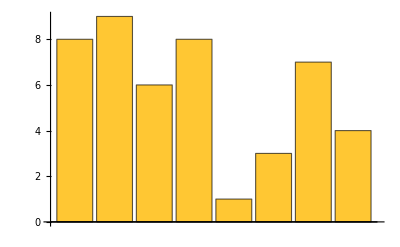

```mathematica
BarChart[{8, 9, 6, 8, 1, 3, 7, 4}]
```

# Este código genera un gráfico de barras con un título y estilo de etiquetas personalizado.
	# Título del gráfico: “Gráfico de Barras”
		# Añade un título al gráfico usando la opción PlotLabel.
		# El título es una expresión que se presenta como “Gráfico de Barras”.
  
	# Estilo de las etiquetas: 
		# Establece el estilo de las etiquetas con un tipo de fuente y tamaño específico.
		# FontFamily -> “Roboto Serif” define el tipo de letra.
		# 20pt es el tamaño de la fuente para las etiquetas.
		# GrayLevel[0] establece el color de las etiquetas a un gris oscuro (nivel de gris 0 es negro).

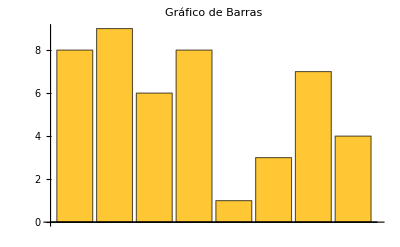

```mathematica
Show[%1,PlotLabel->HoldForm[Gráfico de Barras],LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

# Gráfico de barras en 3D (visual)

```mathematica
BarChart3D[{8, 9, 6, 8, 1, 3, 7, 4}]
```

-Graphics3D-

# Gráfico de barras 3D:
	# Se genera un gráfico de barras en 3D utilizando la función `BarChart3D`.
	# Los valores de las barras son: {8, 9, 6, 8, 1, 3, 7, 4}.
	# Estos valores representan la altura de cada barra en el gráfico 3D.

# Configuración de la forma de las barras:
	# La opción `ChartElementFunction -> “Cylinder”` modifica la forma de las barras.
	# En lugar de las barras rectangulares estándar, se utiliza la forma de cilindro.

```mathematica
BarChart3D[{8,9,6,8,1,3,7,4},ChartElementFunction->"Cylinder"]
```

-Graphics3D-

# Gráfico de pastel 2D

```mathematica
PieChart[{8, 9, 6, 8, 1, 3, 7, 4}]
```

-Graphics-

# Gráfico de pastel 2D
	# Se genera un gráfico de tarta (pie chart) con los valores: {8, 9, 6, 8, 1, 3, 7, 4}.
	# Estos valores representan el tamaño de cada sector en la gráfica.

# Función de elementos de gráfico:
	# La opción `ChartElementFunction -> “SquareWaveSector”` cambia la forma de los sectores del gráfico.
	# En lugar de los sectores tradicionales, se utiliza una forma tipo “SquareWave” (onda cuadrada) para los sectores.

# Leyendas del gráfico:
	# `ChartLegends` se usa para añadir leyendas a los sectores.
	# Se asignan etiquetas a cada sector, como “Rojo”, “Morado”, “Verde”, etc.
	# Cada leyenda está estilizada con un color específico (Red, Purple, Green, etc.), utilizando la función `Style` para dar formato a los textos.

# Estilo de los sectores:
	# `ChartStyle` define los colores de cada sector en el gráfico.
	# Los colores asignados son: Red, Purple, Green, Blue, Orange, Yellow, Purple, Gray.
	# Esto cambia el color de cada sector para que coincidan con las leyendas correspondientes.

```mathematica
PieChart[{8,9,6,8,1,3,7,4},ChartElementFunction->"SquareWaveSector",ChartLegends->{Style["Rojo",Red],Style["Morado",Purple],Style["Verde",Green],Style["Azul",Blue],Style["Naranja",Orange],Style["Amarillo",Yellow],Style["Violeta",Purple],Style["Gris",Gray]},ChartStyle->{Red,Purple,Green,Blue,Orange,Yellow,Purple,Gray}]
```

-Graphics-

# Gráfico de pastel 2D

# Título del gráfico:
	# La opción `PlotLabel` se utiliza para asignar un título al gráfico.
	# El título “Gráfico de Pastel” es mostrado en el gráfico.
	# Se usa `HoldForm` para evitar que la expresión se evalúe y se muestre tal cual.

# Estilo de las etiquetas:
	# `LabelStyle` configura el estilo visual de las etiquetas del gráfico.
	# `FontFamily -> “Roboto Serif”` define la fuente a utilizar en las etiquetas.
	# `20pt` es el tamaño de la fuente para las etiquetas.
	# `14` es el tamaño de la fuente para el texto de las etiquetas.
	# `GrayLevel[0]` define el color de las etiquetas como negro.
	# `Bold` aplica el estilo en negrita a las etiquetas, haciendo que el texto se destaque.

```mathematica
Show[%11,PlotLabel->HoldForm[Gráfico de Pastel],LabelStyle->{FontFamily->"Roboto Serif 20pt",14,GrayLevel[0],Bold}]
```

-Graphics-

# Gráfico de pastel en 3D;efecto visual,no recomendado para análisis

```mathematica
PieChart3D[{8, 9, 6, 8, 1, 3, 7, 4}]
```

-Graphics3D-

# Gráfico de tarta 3D:
	# Se genera un gráfico de tarta 3D utilizando la función `PieChart3D`.
	# Los valores de las porciones son: {8, 9, 6, 8, 1, 3, 7, 4}.
	# Cada valor representa el tamaño de una porción del gráfico 3D.

# Función de los elementos de gráfico:
	# `ChartElementFunction -> “CylindricalSector3D”` cambia la forma de los sectores a una forma cilíndrica 3D.
	# Esto crea una visualización tridimensional de los sectores con una forma cilíndrica.

# Estilo de los sectores:
	# `ChartStyle` define los colores de cada sector en el gráfico 3D.
	# Los colores asignados son: Red, Purple, Green, Blue, Orange, Yellow, Cyan, Gray.
	# Cada uno de estos colores corresponde a una de las porciones del gráfico.

# Leyendas del gráfico:
	# `ChartLegends` se utiliza para agregar leyendas personalizadas.
	# Las leyendas indican el color de cada sector, con los nombres: “Rojo”, “Morado”, “Verde”, etc.

```mathematica
PieChart3D[{8,9,6,8,1,3,7,4},ChartElementFunction->"CylindricalSector3D",ChartStyle->{Red,Purple,Green,Blue,Orange,Yellow,Cyan,Gray},ChartLegends->{"Rojo","Morado","Verde","Azul","Naranja","Amarillo","Cian","Gris"}]
```

-Graphics3D-

💎 Nota: los gráficos 3D son vistosos pero menos precisos para interpretación cuantitativa; para reportes prefiero 2D con etiquetas claras (ChartLabels, PlotLegends).

## 5.2. Selección y manipulación de datos para visualización

📌 Explicación:  funciones para preparar subconjuntos de datos antes de graficar (Take, Drop, Reverse) y trazados auxiliares (NumberLinePlot, Column).

# Devuelve la lista de dígitos de 1988:{1,9,8,8}

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

# Devuelve el último dígito:8

```mathematica
Last[IntegerDigits[1988]]
```

8

# Invierte la lista de dígitos

```mathematica
Reverse[IntegerDigits[1988]]
```

{8,8,9,1}

# Toma los primeros 4 elementos

```mathematica
Take[{101, 203, 401, 602, 332, 412}, 4]
```

{101,203,401,602}

# Elimina los primeros 4 elementos,devuelve el resto

```mathematica
Drop[{101, 203, 401, 602, 332, 412}, 4]
```

{332,412}

# Dibuja puntos en una recta numérica (útil para eventos)

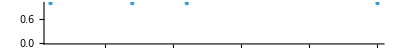

```mathematica
NumberLinePlot[{1, 7, 11, 25}]
```

# Dibuja puntos en una recta numérica (mejorado)

# Ejes del gráfico:
	# La opción `AxesLabel -> {HoldForm[t], None}` se utiliza para etiquetar los ejes.
	# El eje x está etiquetado con “t”, mientras que el eje y no tiene etiqueta (None).
	# `HoldForm` evita que el símbolo de “t” se evalúe y se presenta tal cual.

# Título del gráfico:
	# La opción `PlotLabel -> HoldForm[Crecimiento Bacteriano]` añade un título al gráfico.
	# El título “Crecimiento Bacteriano” es mostrado en el gráfico.
	# Se usa `HoldForm` para evitar la evaluación de la expresión y se visualiza directamente.

# Estilo de las etiquetas:
	# `LabelStyle` se utiliza para definir el estilo de las etiquetas del gráfico.
	# `FontFamily -> “Roboto Serif”` especifica la fuente de las etiquetas.
	# `20pt` es el tamaño de la fuente para las etiquetas, haciendo que el texto sea legible.
	# `GrayLevel[0]` pone el color de las etiquetas en negro.
	# `Bold` hace que el texto de las etiquetas sea **negrita**, para darle énfasis.

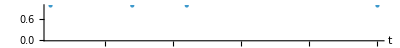

```mathematica
Show[%17,AxesLabel->{HoldForm[t],None},PlotLabel->HoldForm[Crecimiento Bacteriano],LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0],Bold}]
```

# Muestra una columna simple;útil para layout de resultados

```mathematica
Column[{100, 350, 502, 400}]
```

100
350
502
400

💎 Nota: preparar la lista (filtrar, normalizar) antes de graficar para evitar picos que deformen la escala. 
Usa PlotRange -> All si quieres incluir todos los valores.

# Lista de tres gráficos de pastel:1 pequeño (3 sectores),2 (10 sectores), 3 (20 sectores)
# Para presentar estos gráficos lado a lado conviene usar GraphicsRow[{...}] o GraphicsGrid

```mathematica
{PieChart[Range[3]], PieChart[Range[10]], PieChart[Range[20]]}
```

{-Graphics-,-Graphics-,-Graphics-}

# BarChart: Lista de tres gráficos de barras

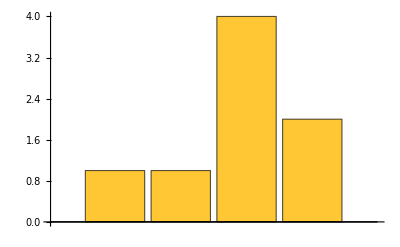
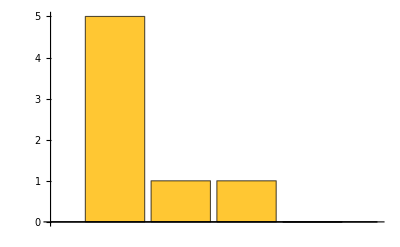
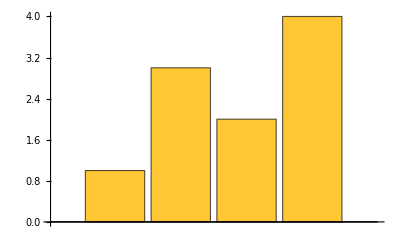

```mathematica
{BarChart[{1, 1, 4, 2}], BarChart[{5, 1, 1, 0}], BarChart[{1, 3, 2, 4}]}
```

## 5.3. Colores y estilos gráficos (paletas y transformaciones)

📌 Explicación: funciones para generar y transformar colores: RGBColor, Hue, Blend, RandomColor y herramientas para aplicar estilos a textos y gráficos.

# Lista de colores predefinidos

```mathematica
{Red, Green, Blue, Purple, Orange, Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0],GrayLevel[0]}

# Invierte el color azul (negativo) --> Escala cromática

```mathematica
ColorNegate[Blue]
```

RGBColor[1., 1., 0.]

# *Mezcla de colores:amarillo+rojo

```mathematica
Blend[{Yellow, Red}]
```

RGBColor[1, Rational[1, 2], 0]

# Color RGB puro (rojo)

```mathematica
RGBColor[{1, 0, 0}]
```

RGBColor[{1, 0, 0}]

# Color por tono en el espacio HSL

```mathematica
Hue[0.5]
```

Hue[0.5]

# Genera un color aleatorio;útil para pruebas

```mathematica
RandomColor[]
```

RGBColor[0.0378617177385101, 0.41743240473723553, 0.0739950800072493]

# Aplica estilo de color a un texto/número

```mathematica
Style[100, Blue]
```

100

# Texto con tamaño grande

```mathematica
Style[100, 50]
```

100

🎯  Reto en clase — Estilos
Probar diferentes estilos en texto y números.

```mathematica
?Style
```

# Aplica un estilo al número 100 con color naranja,cursiva y tamaño de fuente 32

```mathematica
Style[100, {Orange, Italic, 32}]
```

100

# Aplica un estilo al número 70 con negrita,color rojo,subrayado y tamaño de fuente 20

```mathematica
Style[70, {Bold, Red, Underlined, 20}]
```

70

# Estiliza el texto “Mathematics” con un tamaño de fuente mayor,color púrpura, negrita y tipo de letra

```mathematica
Style["Mathematics",{Larger,Purple,Bold,FontFamily->"Roboto Serif 20pt"}]
```

Mathematics

💎 Nota: define una paleta al inicio, por ejemplo pal = {RGBColor[...], RGBColor[...], ...}; y úsala en las gráficas con ColorFunction o ChartStyle para consistencia visual.

## 5.4. Funciones matemáticas básicas y plots elementales

📌 Explicación: evaluación numérica de funciones elementales (coseno, seno), uso de N para aproximaciones y graficado simple con opciones (PlotTheme, PlotRange, AxesLabel).

# Coseno de 0->1

```mathematica
Cos[0]
```

1

# Seno de 0->0

```mathematica
Sin[0]
```

0

# Coseno de π->-1

```mathematica
Cos[Pi]
```

-1

# Forma numérica de Cos[Pi]

```mathematica
N[Cos[π]]
```

-1.

# Aproximación numérica de 10/3

```mathematica
N[10/3]
```

3.33333

# ‘%’ Toma el valor del resultado anterior

```mathematica
%+1
```

4.33333

# Aproximación de Sin(pi/12) con 21 dígitos de precisión

```mathematica
N[Sin[π/12], 21]
```

0.258819045102520762349

# Usa Degree para ángulos en grados

```mathematica
N[Sin[45 Degree]]
```

0.707107

# Salida en radianes

```mathematica
ArcCos[0]
```

π/2

# Tranformación con para salida en grados

```mathematica
N[ArcCos[0]*180/π]
```

90.

🎯 Reto en Clase — Conversión
Input --> Output
rad --> grad (sin conversiones solo con la función Degree)

Entregar la salida del ‘Arccos.08[0]’ en grados

```mathematica
?Degree
```

# Tranformación con “Degree” para salida en grados

```mathematica
N[ArcCos[0]/Degree]
```

90.

# Salida de radianes --> racional

```mathematica
Cos[π/6]
```

(√3)/2

# Salida de radianes --> irracional “N”

```mathematica
N[Cos[π/6]]
```

0.866025

```mathematica
Tan[π/4]
```

1

# Grafica seno en 0..2π

```mathematica
Plot[Sin[x], {x, 0, 2π}]
```

-Graphics-

# Título de la gráfica
# PlotLabel -> “Gráfica de la función Seno”,

# Etiquetas de los ejes
# AxesLabel -> {“x”, “f(x)”},

# Color de la línea de la gráfica
# PlotStyle -> Blue,

# Ticks automáticos en ambos ejes
# Ticks -> {Automatic, Automatic},

# Añadir marco alrededor de la gráfica
# Frame -> True,

# Líneas de la cuadrícula
# GridLines -> Automatic,

# Etiquetas para el marco de la gráfica
# FrameLabel -> {“x”, “f(x)”},

# Ticks automáticos en el marco
# FrameTicks -> {Automatic, Automatic},

# Asegura que toda la función esté visible
# PlotRange -> All

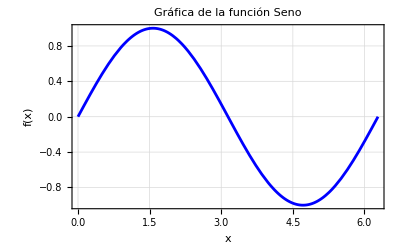

```mathematica
Plot[Sin[x],{x,0,2 π},PlotLabel->"Gráfica de la función Seno",AxesLabel->{"x","f(x)"},PlotStyle->Blue,GridLines->Automatic,Ticks->{Automatic,Automatic},Frame->True,FrameLabel->{"x","f(x)"},FrameTicks->{Automatic,Automatic},PlotRange->All  ]
```

# Grafica coseno en 0..2π

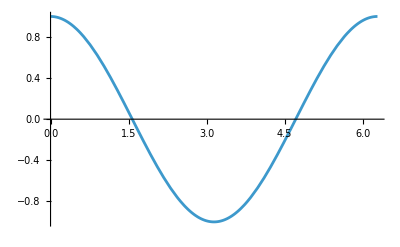

```mathematica
Plot[Cos[x], {x,  0, 2Pi}]
```

# Título de la gráfica
# PlotLabel -> “Gráfica de la función Coseno”,

# Etiquetas de los ejes
# AxesLabel -> {“x”, “f(x)”},

# Color de la línea de la gráfica
# PlotStyle -> Red,

# Ticks automáticos en ambos ejes
# Ticks -> {Automatic, Automatic},

# Añadir marco alrededor de la gráfica
# Frame -> True,

# Líneas de la cuadrícula
# GridLines -> Automatic,

# Etiquetas para el marco de la gráfica
# FrameLabel -> {“x”, “f(x)”},

# Ticks automáticos en el marco
# FrameTicks -> {Automatic, Automatic},

# Asegura que toda la función esté visible
# PlotRange -> All

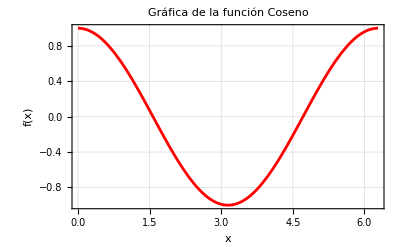

```mathematica
Plot[Cos[x],{x,0,2 π},PlotLabel->"Gráfica de la función Coseno",AxesLabel->{"x","f(x)"},PlotStyle->Red,GridLines->Automatic,Ticks->{Automatic,Automatic},Frame->True,FrameLabel->{"x","f(x)"},FrameTicks->{Automatic,Automatic},PlotRange->All]
```

💎 Nota: usar AxesLabel -> {HoldForm[x], HoldForm[f(x)]} y ImageSize -> Large para gráficos más presentables al exportar.

🎯 Reto en clase — Funciones trigonométricas normales e inversas
Graficar múltiples funciones trigonométricas en un solo plot; para las funciones inversas conviene limitar dominio/rango para evitar valores complejos o discontinuidades.

Gráficas de Funciones Trigonométricas

# Definir lista de funciones trigonométricas normales

```mathematica
trigonometric = {Sin[x], Cos[x], Tan[x], Sec[x], Csc[x], Cot[x]}
```

{Sin[x],Cos[x],Tan[x],Sec[x],Csc[x],Cot[x]}

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles

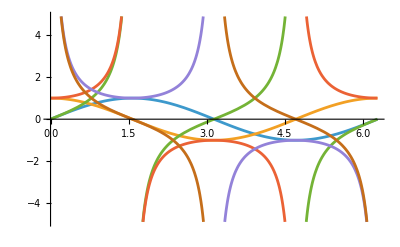

```mathematica
Plot[trigonometric, {x, 0, 2Pi}]
```

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles (mejorado)

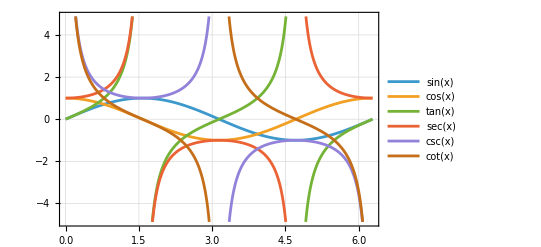

```mathematica
Plot[trigonometric,{x,0,2 π},PlotTheme->"Detailed"]
```

Gráficas de Funciones Trigonométricas Inversas

# Definir lista de funciones trigonométricas inversas

```mathematica
invTri = {ArcSin[x], ArcCos[x], ArcTan[x], ArcSec[x], ArcCsc[x], ArcCot[x]}
```

{ArcSin[x],ArcCos[x],ArcTan[x],ArcSec[x],ArcCsc[x],ArcCot[x]}

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles

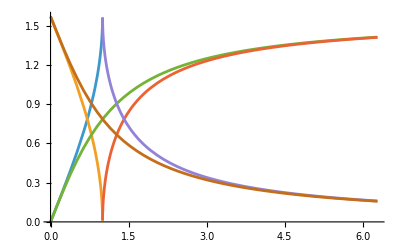

```mathematica
Plot[invTri, {x, 0, 2Pi}]
```

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles (mejorado)

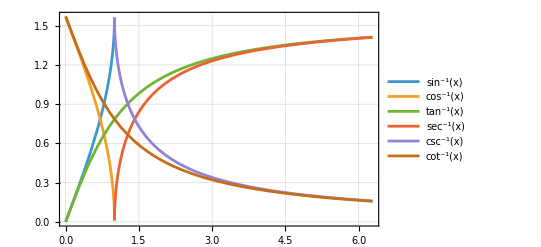

```mathematica
Plot[invTri,{x,0,2 π},PlotTheme->"Detailed"]
```

💎 Nota: al exportar gráficos para informes use ImageSize->Large y Export con formato PNG o PDF; incluye títulos y etiquetas claras (AxesLabel, PlotLabel) y una leyenda (PlotLegends).

```mathematica
CellPrint[Cell["","PageBreak",CellVisible->False]]
```

## 6. Tareas

⚡ Instrucciones: En esta sección se agrupan las tareas asignadas.

## 6.1. Tarea 1 — Cálculos Numéricos y Funciones en Mathematica

📆 2025/09/23

1. Calcular 1 + 2 + 3.

```mathematica
1+2+3
```

6

2. Sumar los números 1, 2, 3, 4, 5.

```mathematica
Total[Range[5]]
```

15

3. Multiplicar los números 1, 2, 3, 4, 5.

```mathematica
1×2×3×4×5
```

120

4. Calcular 5 al cuadrado.

```mathematica
5^2
```

25

5. Calcular 3 elevado a la cuarta potencia.

```mathematica
3^4
```

81

6. Calcular 10 elevado a la potencia 12.

```mathematica
10^12
```

1000000000000

7. Calcular 3 elevado a la potencia 7 × 8.

```mathematica
3^(7×8)
```

523347633027360537213511521

8. Colocar los paréntesis necesarios para que 4 − 2 × 3 + 4 sea igual a 14.

```mathematica
(4-2)×(3+4)
```

14

9. Calcular veintinueve mil multiplicado por setenta y tres.

```mathematica
29000*73
```

2117000

10. Sumar los enteros entre -3 y +3.

```mathematica
Total[Range[-3, 3]]
```

0

11. Calcule 7+6+5 usando la función Plus.

```mathematica
Plus[7,6,5]
```

18

12. Calcule 2×(3+4) usando Times y Plus.

```mathematica
Times[2, Plus[3,4]]
```

14

13. Utilice Max para encontrar el máximo entre 6×8 y 5×9.

```mathematica
Max[Times[6, 8], Times[5, 9]]
```

48

14. Use RandomInteger para generar un número aleatorio entre 0 y 1000.

```mathematica
RandomInteger[{0, 1000}]
```

880

15. Use Plus y RandomInteger para generar un número entre 10 y 20.

```mathematica
Plus[10, RandomInteger[{0, 10}]]
```

13

16. Calcule 5×4×3×2 usando Times.

```mathematica
Times[5, 4, 3, 2]
```

120

17. Calcule 2−3 usando Subtract.

```mathematica
Subtract[2, 3]
```

-1

18. Calcule (8+7)*(9+2) usando Times y Plus.

```mathematica
Times[Plus[8, 7], Plus[9, 2]]
```

165

19. Calcule (26−89)/9 usando Subtract y Divide.

```mathematica
Divide[Subtract[26, 89], 9]
```

-7

20. Calcule 100 − 5^2 usando Subtract y Power.

```mathematica
Subtract[100, Power[5,2]]
```

75

21. Encuentre el mayor entre 3^5 y 5^3.

```mathematica
Max[Power[3, 5], Power[5, 3]]
```

243

## 6.2. Tarea 2 — Formato de Notebook

📅 2025/09/26

La Tarea 2 consiste en dar formato al cuaderno de Mathematica y mejorar la presentación de las gráficas. El objetivo es aplicar estilos a las celdas, como la personalización de fuentes, colores y márgenes, para hacer el documento más legible y profesional. Además, se deben mejorar las gráficas añadiendo etiquetas a los ejes, títulos, leyendas y ajustando el estilo de las líneas para facilitar su interpretación. Se debe asegurar que las funciones sean visibles y claras, utilizando un formato visual coherente y atractivo en todo el cuaderno.

## 7. Apéndice

## 7.1 Comandos Comunes

🔋 Capturas de imagen

CurrentImage[] — Captura una imagen desde la cámara y devuelve un objeto Image.

FacialFeatures[imagen] — Detecta y devuelve los rasgos faciales de una imagen.

🔧 Sistema y directorios

SetDirectory[“path”] — Cambia el directorio de trabajo.

Sin argumentos abre un selector o muestra el directorio actual.

Date[] — Devuelve la fecha y hora actual del sistema.

🔊 Interactividad

Speak[“texto”] — Convierte texto a voz (requiere soporte de audio).

Button[“etiqueta”, acción] — Crea un botón interactivo que ejecuta una acción al presionar.

🌍 Entidades (Knowledgebase)

Entity[“Country”,”Cod”] — Representa un país en la base de conocimiento.

EntityValue[entidad,”Flag”] — Extrae información asociada (ej. banderas).

EntityList[EntityClass[“Planet”,All]] — Lista todas las entidades de tipo planeta.

📏 Magnitudes y conversiones

Quantity[v,”Units”] — Representa magnitudes físicas con unidades.

UnitConvert[Quantity[..., u1], u2] — Convierte entre unidades compatibles.

UnitSimplify[Quantity[...]] — Simplifica una expresión con unidades.

CurrencyConvert[Quantity[x,”From”],Quantity[1,”To”]] — Conversión monetaria (requiere conectividad).

📋 Listas

Clear[símbolo] — Limpia la definición de un símbolo.

Range[n] — Genera una lista del 1 al n.

Join[list1,list2,...] — Une listas.

Reverse[list] — Invierte una lista.

MemberQ[list,elem] — Verifica si un elemento está en la lista.

Sort[list] — Ordena los elementos.

Length[list] — Devuelve la longitud de la lista.

Total[list] — Suma los elementos de la lista.

Count[list,patrón] — Cuenta cuántos elementos cumplen un patrón.

First[list], Last[list] — Extrae el primer o último elemento.

📊 Gráficas

ListPlot[list] — Representa gráficamente valores de una lista.
BarChart[list], BarChart3D[list] — Barras en 2D/3D.
PieChart[list], PieChart3D[list] — Gráficos de pastel en 2D/3D.
NumberLinePlot[list] — Marca valores en una recta numérica.
Column[{...}] — Organiza elementos en columna.

🔢 Funciones matemáticas

Cos[x], Sin[x], Tan[x], Sec[x], Csc[x], Cot[x] — Funciones trigonométricas.

ArcSin[x], ArcCos[x], ArcTan[x], ArcSec[x], ArcCsc[x], ArcCot[x] — Funciones trigonométricas inversas.

Plot[expr,{x,a,b}] — Grafica una función en un intervalo.

Show[graf1,graf2,...] — Superpone gráficos, permite etiquetas.

N[expr] — Evalúa en forma numérica (decimal). Ej.: N[10/3] → 3.3333.

% — Hace referencia a la salida anterior.

🔢 Números y dígitos

IntegerDigits[n] — Devuelve los dígitos de un número en lista.

Min[list], Max[list] — Extrae el mínimo o máximo de una lista.

RandomInteger[n] — Genera un entero aleatorio.

🎨 Estilos y colores

RandomColor[] — Genera un color aleatorio.

Style[expr,opts] — Cambia estilo de un objeto (color, tamaño, etc.).

RGBColor[{r,g,b}], Hue[h], Blend[{c1,c2}], ColorNegate[c] — Definición y manipulación de colores.

📐 Notas adicionales

Cuando se suman o combinan Quantity con diferentes unidades, Mathematica intenta convertir automáticamente al sistema más coherente.

N es muy útil para obtener valores decimales en lugar de fracciones exactas.

La variable % guarda el último output y se puede encadenar en cálculos.